# Error Bounds in The Jacobi and Gauss Seidel Methods

In this notebook we will take a look the error bounds for iterative matrix methods and write an iteration module!

Let’s look at the following example. We will see why it is interesting later.

```mathematica
A={{2,-1,1},{2,2,2},{-1,-1,2}};
A//MatrixForm
```

(2 | -1 | 1
2 | 2 | 2
-1 | -1 | 2)

```mathematica
b={-1,4,-5};
MatrixForm[b]
```

(-1
4
-5)

We will need the actual solution later when we look at error bounds, so let’s just go ahead and compute it now.

```mathematica
sol=LinearSolve[A,b]
```

{1,2,-1}

Now we need to decompose a matrix into D, L, and U and we will write a function to do this for us. So we can make sure that it works let’s look at the same matrix and vector from our previous examples.

Getting the diagonal entries is pretty straight forward.

```mathematica
Di[A_]:=DiagonalMatrix[Table[A[[i,i]],{i,1,Length[A]}]];
Di[A]//MatrixForm
```

(2 | 0 | 0
0 | 2 | 0
0 | 0 | 2)

Getting U is a little bit trickier, but the following will get it done.

```mathematica
?PadLeft
```

```mathematica
U[A_]:=-Table[PadLeft[Table[A[[i,j]],{j,i+1,Length[A]}],Length[A]],{i,1,Length[A]}]
U[A]//MatrixForm
```

(0 | 1 | -1
0 | 0 | -2
0 | 0 | 0)

Luckily, we can just use the U code to get L!

```mathematica
L[A_]:=Transpose[U[Transpose[A]]]
L[A]//MatrixForm
```

(0 | 0 | 0
-2 | 0 | 0
1 | 1 | 0)

Let’s just make sure we did it right!

```mathematica
Di[A]-L[A]-U[A]-A//MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

Now we define the matrices Tj and Tg for the Jacobi and Gauss-Seidel methods.

```mathematica
Tj[A_]:=Inverse[Di[A]].(L[A]+U[A]);
Tj[A]//MatrixForm
```

(0 | 1/2 | -1/2
-1 | 0 | -1
1/2 | 1/2 | 0)

```mathematica
Tg[A_]:=Inverse[Di[A]-L[A]].U[A];
Tg[A]//MatrixForm
```

(0 | 1/2 | -1/2
0 | -1/2 | -1/2
0 | 0 | -1/2)

Here is the vector c for the Jacobi and Gauss-Seidel methods.

```mathematica
cj[A_,b_]:=Inverse[Di[A]].b;
cj[A,b]//MatrixForm
```

(-1/2
2
-5/2)

```mathematica
cg[A_,b_]:=Inverse[Di[A]-L[A]].b;
cg[A,b]//MatrixForm
```

(-1/2
5/2
-3/2)

Our goal is to look at the error bounds for the iteration. Luckily, Mathematica is happy to compute matrix norms for us!

### Computing Matrix Norms in Mathematica

We can compute the l_2 norm with the following command.

```mathematica
Norm[A,2]
```

√Root[-324+163 #1-24 #1^2+#1^3&,3]

Notice that Mathematica returns this norm as pure function and a point at which to evaluate. This is something like returning f(4) as well as what the function f is instead of returning the value. There is some decision making done under the hood... sometimes it will do this and sometimes it won’t (likely when it suspects there will be round-off error). So, if we want the approximation we have to N it.

```mathematica
N[Norm[A,2]]
```

3.74502

For fun, let’s verify that we can compute the l_2 norm in terms of the spectral radius. There is no (that I know of) built in function to get the spectral radius. But, recall that it is just the eigenvalue of largest absolute value. Mathematica can certainly compute eigenvalues, so we can get the spectral radius with the following function.

```mathematica
SpectralRadius[A_]:=N[Max[Abs[Eigenvalues[A]]]];
```

```mathematica
SpectralRadius[A]
```

3.

By a theorem from the other day we can compute the l_2 norm as follows.

```mathematica
l2[A_]:=N[Sqrt[SpectralRadius[Transpose[A].A]]];
```

Let’s see if it works!

```mathematica
l2[A]
```

3.74502

If we want the l_∞ norm:

```mathematica
Norm[A,Infinity]
```

6

Remember the l_∞ norm is just the max of the sums of absolute values along each row, so Mathematica just returns the value

### Matrix Iteration Error Bounds

Now let’s take a look at the error bounds. Before we get started let’s take a look at the l_2 norm of Tj ang Tg.

```mathematica
SpectralRadius[Tj[A]]
```

1.11803

```mathematica
N[Norm[Tj[A],2]]
```

1.5

```mathematica
SpectralRadius[Tg[A]]
```

0.5

```mathematica
N[Norm[Tg[A],2]]
```

0.866025

This looks like bad news for the Jacobi method and we shouldn’t expect good results, but the Gauss-Seidel method should do pretty well. Let’s take a look.

Now let’s make some plots to be sure the error bounds work. First we will define some functions to compute the error bounds and the actual bounds.

```mathematica
ErrorBound2[T_,x_,x0_,k_]:=N[Norm[T,2]^k*Norm[x-x0,2],100];
ErrorBoundInf[T_,x_,x0_,k_]:=N[Norm[T,Infinity]^k*Norm[x-x0,Infinity],100];
ActualError2[xk_,x_]:=N[Norm[x-xk,2],100];
ActualErrorInf[xk_,x_]:=N[Norm[x-xk,Infinity],100];
```

To actually perform the iteration we use the same code as before:

```mathematica
It[{x_,T_,c_}]:={T.x+c,T,c};
```

```mathematica
Data=Table[N[Nest[It,{Table[0,{i,1,Length[A]}],Tj[A],cj[A,b]},i]][[1]],{i,1,20}];
```

Let’s look at the story for the l_2 norm.

```mathematica
ErrorBound2Data=Table[ErrorBound2[Tj[A],sol,Table[0,{i,1,Length[A]}],i],{i,1,20}];
ActualError2Data=Table[ActualError2[Data[[i]],sol],{i,1,20}];
```

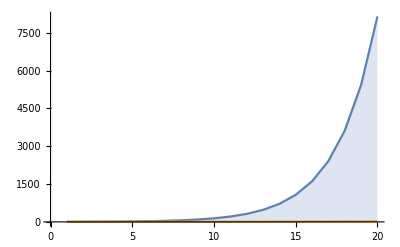

```mathematica
ListLinePlot[{ErrorBound2Data,ActualError2Data},Filling->Axis,PlotRange->All]
```

Well, the error bound is blowing up... why? Is the method still converging though?

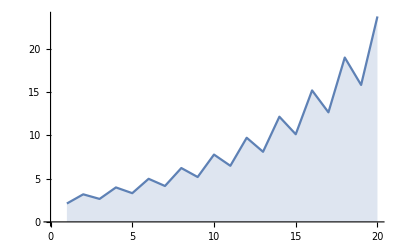

```mathematica
ListLinePlot[ActualErrorData,Filling->Axis,PlotRange->All]
```

Nope! The l_∞ norm situation is similar, so let’s just move on to the Gauss-Seidel method.

```mathematica
Data=Table[N[Nest[It,{Table[0,{i,1,Length[A]}],Tg[A],cg[A,b]},i],100][[1]],{i,1,20}];
```

Again, we collect the error data. This time we will get both the l_2 norm and the l_∞ norm bounds.

```mathematica
ErrorBound2Data=Table[ErrorBound2[Tg[A],sol,Table[0,{i,1,Length[A]}],i],{i,1,20}];
ErrorBoundInfData=Table[ErrorBoundInf[Tg[A],sol,Table[0,{i,1,Length[A]}],i],{i,1,20}];
ActualError2Data=Table[ActualError2[Data[[i]],sol],{i,1,20}];
ActualErrorInfData=Table[ActualErrorInf[Data[[i]],sol],{i,1,20}];
```

We should expect things to go better because Tg has l_2 norm less than 1.

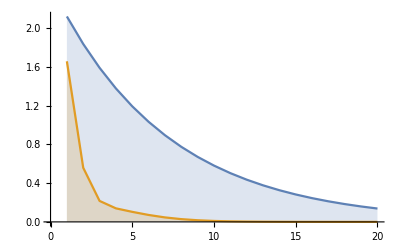

```mathematica
ListLinePlot[{ErrorBound2Data,ActualError2Data},Filling->Axis,PlotRange->All]
```

And indeed things look pretty good. One thing to note is that the error bounds are not very sharp. The method does much better than the bound at every step.


What about the l_∞ norm bounds?

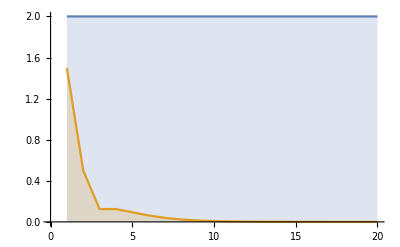

```mathematica
ListLinePlot[{ErrorBoundInfData,ActualErrorInfData},Filling->Axis,PlotRange->All]
```

This looks odd... whats going on?

```mathematica
N[Norm[Tg[A],Infinity]]
```

1.

Aha! The l_∞ norm of Tg is 1 so our error bound theorem can’t be applied... but notice the method still converges in this norm. The error bound norm works a bit like the ratio test (and the like) where convergence is only guaranteed if the norm is less than 1, but the method could still converge if the norm equals 1.